# Reheaton Decays - Attempt 1

## Inputs

```mathematica
Clear[matSq,c1,c2,grhh,r11,r22,w11,w22,w12,mr,mZ,mW]
r ;
ourHiggs = 125;
m =Sqrt[2]* Sqrt[(2*(-1) +r)*-ourHiggs^2/(2r)];
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (boson)
p2= Momentum of 2nd out-going particle (boson)
mr= Mass of the decaying reheaton
m = Mass of the higgs
grhh= Reheaton-higgs coupling
α = Fine structure constant
x and y are Feynman parameters

## Reheaton to ww

Note: The factor of 1/9 is present to remove the simple colour sum of a higgs-squark loop diagram from my old project.  The 3/4 is the proper SU(2) colour factor of the diagram.

```mathematica
matSq =(3/4)*(1/9)*Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mw1,4],Times[Power[mw1,2],Plus[Times[4,Power[mw2,2]],Times[-2,Power[mr,2]]]],Power[Plus[Power[mw2,2],Times[-1,Power[mr,2]]],2]]],Times[6,c1,c2,Plus[Power[mw1,2],Power[mw2,2],Times[-1,Power[mr,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]](*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details. Adjustments for the differences between the cases are in front of the "Times[]" bracket and are commented on here.*)
```

(3 (c2^2 (mw1^4+(-mr^2+mw2^2)^2+mw1^2 (-2 mr^2+4 mw2^2))+6 c1 c2 (-mr^2+mw1^2+mw2^2) mZ^2+8 c1^2 mZ^4))/(8 v^2)

The c1 on-shell term is zero.

Note: This calculation is taken from my squark loop work, as such the (9/4) is to ultimately cancel the electromagnetic change of 2/3 associated with the squarks.

```mathematica
c2LOwwInted = (9/4)*2*(Rational[1, 18]*g^2*grhh*v*
     (mr^2 - 4*m1^2*ArcTan[mr*1/Sqrt[4*m1^2 - mr^2]]^2))/(mr^4*Pi^2)
```

(g^2 grhh v (mr^2-4 m1^2 ArcTan[mr/(√(4 m1^2-mr^2))]^2))/(4 mr^4 π^2)

## Coupling definitions

Explicitly, we can write out the couplings in terms of an unbroken SU(2) theory.

#### Higgs couplings

```mathematica
r11= a
```

a

```mathematica
r22 = a
```

a

```mathematica
SUBIN[reheatonMass_,higgsMass_,a_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
g-> e/sW,
Alfa->1/128,Alfa2->(1/128)^2,
Alfas->0.12,Alfas2-> (0.12^2),
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],gs-> Sqrt[(4*Pi*Alfas)],
m1->m,m2->m,
At-> ((xt/mt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[reheatonMass_,higgsMass_,a_]:=matToSub//.SUBIN[reheatonMass,higgsMass,a]//Simplify
```

## Plug in values

```mathematica
c1 = 0//. grhh-> r11//.M1->mw1^2//.M2->mw2^2
```

0

```mathematica
c2 =c2LOwwInted //. grhh-> r11//.M1->mw1^2//.M2->mw2^2
```

(a g^2 v (mr^2-4 m1^2 ArcTan[mr/(√(4 m1^2-mr^2))]^2))/(4 mr^4 π^2)

```mathematica
matSq
```

(3 a^2 g^4 (mw1^4+(-mr^2+mw2^2)^2+mw1^2 (-2 mr^2+4 mw2^2)) (mr^2-4 m1^2 ArcTan[mr/(√(4 m1^2-mr^2))]^2)^2)/(128 mr^8 π^4)

## Reheaton to two fermions (our sector)

```mathematica
decayWidthUs = (a^2/(8Pi))*(mr/(mh^2)^2)*(3*(mb^2)(1-4mb^2/mr^2)^(3/2) +3*(mc^2)(1-4mc^2/mr^2)^(3/2)+(mtau^2)(1-4mtau^2/mr^2)^(3/2))
```

(a^2 mr (3 mb^2 (1-(4 mb^2)/mr^2)^(3/2)+3 mc^2 (1-(4 mc^2)/mr^2)^(3/2)+mtau^2 (1-(4 mtau^2)/mr^2)^(3/2)))/(8 mh^4 π)

```mathematica
decayWidthUs = decayWidthUs /.mb->4.18 /.mc->1.29 /.mtau -> 1.78 /.mh-> 125
```

(a^2 (52.4172 (1-69.8896/mr^2)^(3/2)+3.1684 (1-12.6736/mr^2)^(3/2)+4.9923 (1-6.6564/mr^2)^(3/2)) mr)/(1953125000 π)

## Results

```mathematica
matSqResult = matSq//.SUBIN[reheatonMass,higgsMass,a]//Simplify
```

(0.0000438324 a^2 (mr^4+mw1^4+4 mw1^2 mw2^2+mw2^4-2 mr^2 (mw1^2+mw2^2)) (mr^2+(62500 (-2+r) ArcTan[mr/(√(-mr^2-(62500 (-2+r))/r))]^2)/r)^2)/mr^8

```mathematica
matSqResultOS = Chop[matSqResult/. mw1->0/.mw2->0/.r->1](*Put W bosons mass to zero*)
```

(0.0000438324 a^2 (mr^2-62500 ArcTan[mr/(√(62500-mr^2))]^2)^2)/mr^4

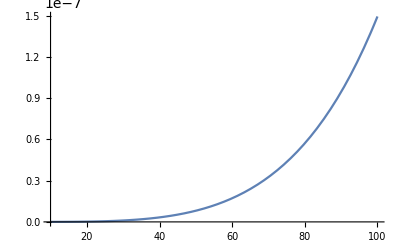

```mathematica
Plot[matSqResultOS/(a^2),{mr,10,100}]
```

```mathematica
decayWidthE = (1/2)*(mr/2)/(8Pi*mr^2) * matSqResultOS
```

(4.36009×10^-7 a^2 (mr^2-62500 ArcTan[mr/(√(62500-mr^2))]^2)^2)/mr^5

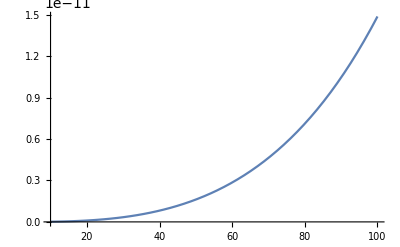

```mathematica
Plot[decayWidthE/(a^2),{mr,10,100}]
```

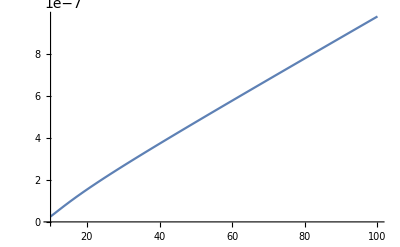

```mathematica
Plot[decayWidthUs/(a^2),{mr,10,100}]
```

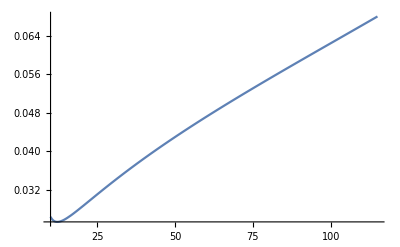

```mathematica
Plot[(decayWidthE/decayWidthUs)^(1/4),{mr,10,115}]
```

# Result

```mathematica
tempRationE1=(decayWidthE/decayWidthUs)^(1/4) /.mr -> 100
```

0.0624494

```mathematica
(decayWidthE/decayWidthUs)//FullForm
```

Times[2675.32,Power[Plus[Times[52.4172,Power[Plus[1,Times[-69.8896,Power[mr,-2]]],Rational[3,2]]],Times[3.1684,Power[Plus[1,Times[-12.6736,Power[mr,-2]]],Rational[3,2]]],Times[4.9923,Power[Plus[1,Times[-6.6564,Power[mr,-2]]],Rational[3,2]]]],-1],Power[mr,-6],Power[Plus[Power[mr,2],Times[-62500,Power[ArcTan[Times[mr,Power[Plus[62500,Times[-1,Power[mr,2]]],Rational[-1,2]]]],2]]],2]]

```mathematica
(decayWidthE/decayWidthUs)
```

(2675.32 (mr^2-62500 ArcTan[mr/(√(62500-mr^2))]^2)^2)/((52.4172 (1-69.8896/mr^2)^(3/2)+3.1684 (1-12.6736/mr^2)^(3/2)+4.9923 (1-6.6564/mr^2)^(3/2)) mr^6)